```mathematica
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

### Real Coulombic part

```mathematica
ReVcpar[r_,mD_,v_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,v,mD]] Exp[-√Re[Πpar[θ,v,mD]]r Cos[θ]],{θ,0,π/2}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45726}. NIntegrate obtained 0.136237+0.286526 ⅈ and 0.0000169628 for the integral and error estimates.

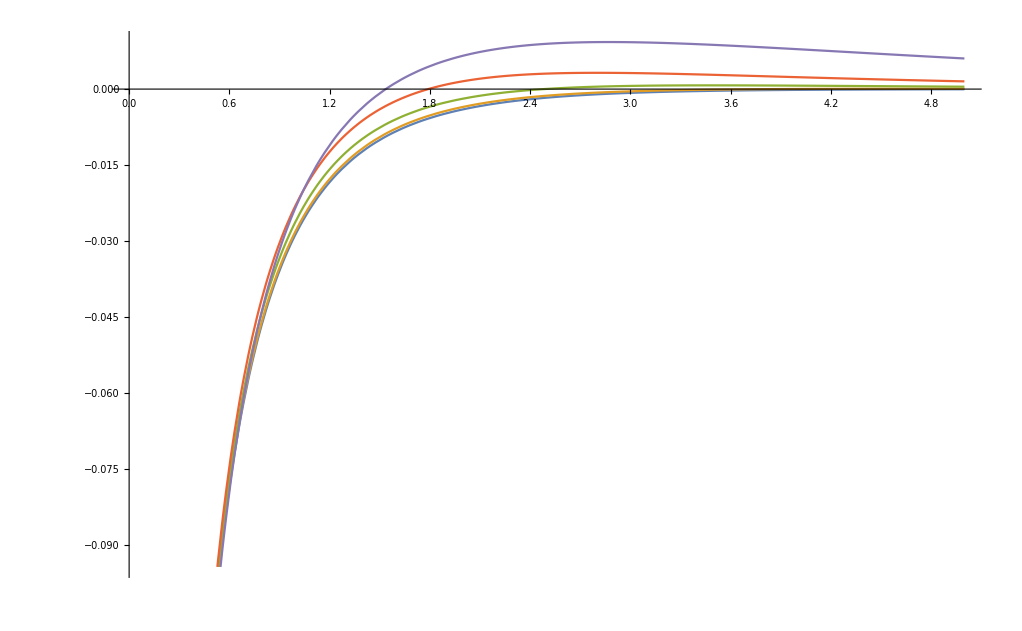

```mathematica
Plot[{ReVcpar[r/0.197,0.25,0.,αcont[[1]]],ReVcpar[r/0.197,0.25,0.2,αcont[[1]]],ReVcpar[r/0.197,0.25,0.4,αcont[[1]]],ReVcpar[r/0.197,0.25,0.6,αcont[[1]]],ReVcpar[r/0.197,0.25,0.8,αcont[[1]]],ReVcpar[r/0.197,0.25,0.99,αcont[[1]]]},{r,0,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45726}. NIntegrate obtained 0.13624+0.286526 ⅈ and 0.0000169628 for the integral and error estimates.

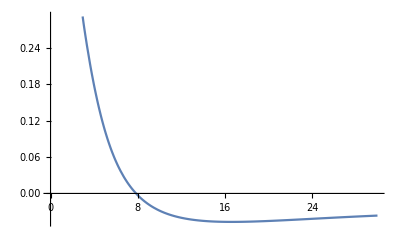

```mathematica
Plot[Re[-1/r Log[r ReVcpar[r,0.25,0.99,αcont[[1]]]]],{r,0,30}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.45726}. NIntegrate obtained 0.13624+0.286526 ⅈ and 0.0000169628 for the integral and error estimates.

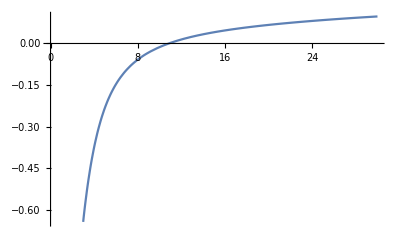

```mathematica
Plot[Im[-1/r Log[r ReVcpar[r,0.25,0.99,αcont[[1]]]]],{r,0,30}]
```

```mathematica
Integrate[f[x,y]DiracDelta[x]DiracDelta[x+a-y],{x,-∞,∞},{y,-∞,∞}]
```

f[0,a]

```mathematica
(*check above formula holds*)
```

```mathematica
ReVcparcheck[r_,mD_,v_,α_]:=α/π NIntegrate[p^2 Sin[θ] Exp[ⅈ r p Cos[θ]]/(p^2+Re[Πpar[θ,v,mD]]),{p,0,∞},{θ,0,π}];
```

### Imaginary Coulombic part

#### misc

```mathematica
Clear[r,θ];
Assuming[θ∈Reals,Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,0,∞}]]//FullSimplify
```

ConditionalExpression[-1/(4 Im[z])ⅈ (2 Cosh[r √z Cos[θ]] CosIntegral[-ⅈ r √z Cos[θ]]-2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]]),((Cos[θ]<0&&Im[r]<0)||(Cos[θ]>0&&Im[r]>0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
Clear[r,θ];
Assuming[θ∈Reals,Integrate[(p Exp[ⅈ p r Cos[θ]])/((p^2+z)(p^2+Conjugate[z])),{p,-∞,0}]]//FullSimplify
```

ConditionalExpression[-1/(4 Im[z])ⅈ (-2 Cosh[r √z Cos[θ]] CosIntegral[ⅈ r √z Cos[θ]]+2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])+2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]-2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]]),((Im[r]>0&&Cos[θ]<0)||(Cos[θ]>0&&Im[r]<0))&&((z≠Re[z]&&Re[√z]≠0&&Re[√Conjugate[z]]≠0)||(Re[√z]>0&&Re[√Conjugate[z]]>0&&Re[z]≥0))]

```mathematica
-1/(4 Im[z])ⅈ (2 Cosh[r √z Cos[θ]] CosIntegral[-ⅈ r √z Cos[θ]]-2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])+1/(4 Im[z])ⅈ (-2 Cosh[r √z Cos[θ]] CosIntegral[ⅈ r √z Cos[θ]]+2 Cosh[r √Conjugate[z] Cos[θ]] CosIntegral[ⅈ r √Conjugate[z] Cos[θ]]+ⅈ π (Sinh[r √z Cos[θ]]-Sinh[r √Conjugate[z] Cos[θ]])+2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]-2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])//FullSimplify
```

-1/(2 Im[z])ⅈ (Cosh[r √z Cos[θ]] (CosIntegral[-ⅈ r √z Cos[θ]]+CosIntegral[ⅈ r √z Cos[θ]])-Cosh[r √Conjugate[z] Cos[θ]] (CosIntegral[-ⅈ r √Conjugate[z] Cos[θ]]+CosIntegral[ⅈ r √Conjugate[z] Cos[θ]])-2 Sinh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]+2 Sinh[r √Conjugate[z] Cos[θ]] SinhIntegral[r √Conjugate[z] Cos[θ]])

```mathematica
r=2;
z=3;
θ=0;
N[CosIntegral[-ⅈ r √z Cos[θ]]+CosIntegral[ⅈ r √z Cos[θ]]]
```

13.5827+0. ⅈ

```mathematica
2 N[CoshIntegral[r √z Cos[θ]]]
```

13.5827

#### sol

```mathematica
ImVcparcheck[r_,mD_,v_,α_,T_]:=-α T mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/((1+v^2 Sin[θ]^2)^(5/2))(p Exp[ⅈ p r Cos[θ]])/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]])),{p,0,∞},{θ,0,π}]
```

```mathematica
ImVcparcheck[10,0.15,0.5,αcont[[1]],0.155]
```

-0.0338686+5.59436×10^-13 ⅈ

```mathematica
ImVcparLT[r_,mD_,v_,α_,T_]:=α T mD^2(1-v^2)^(3/2)NIntegrate[Sin[θ](2+v^2 Sin[θ]^2)/((1+v^2 Sin[θ]^2)^(5/2))1/(ⅈ Im[Πpar[θ,v,mD]])(Sinh[r Cos[θ] √Πpar[θ,v,mD]]SinhIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Cosh[r Cos[θ] √Πpar[θ,v,mD]]CoshIntegral[r Cos[θ] √Πpar[θ,v,mD]]-Sinh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]SinhIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]+Cosh[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]CoshIntegral[r Cos[θ] √Conjugate[Πpar[θ,v,mD]]]),{θ,0,π/2}]
```

```mathematica
ImVcparLT[10,0.15,0.5,αcont[[1]],0.155]
```

-0.0338686-1.81181×10^-18 ⅈ

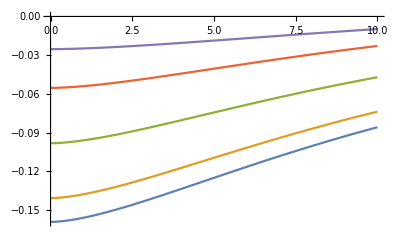

```mathematica
Plot[{Re[ImVcparLT[r,0.15,0.0001,αcont[[1]],0.155]],Re[ImVcparLT[r,0.15,0.2,αcont[[1]],0.155]],Re[ImVcparLT[r,0.15,0.4,αcont[[1]],0.155]],Re[ImVcparLT[r,0.15,0.6,αcont[[1]],0.155]],Re[ImVcparLT[r,0.15,0.8,αcont[[1]],0.155]]},{r,0,10}]
```

```mathematica
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)Sinc[x z],{z,0,∞}]];
```

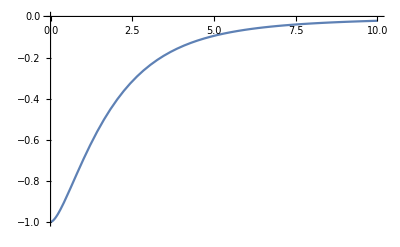

```mathematica
Plot[-ϕ[x],{x,0,10}]
```

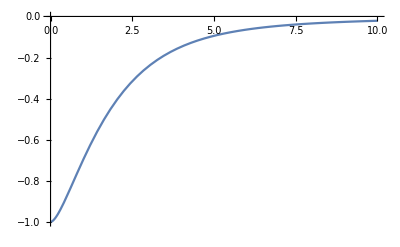

```mathematica
Plot[1/2 Re[ImVcparLT[r,1,0.0001,1,1]],{r,0,10}]
```

### Check quadrants

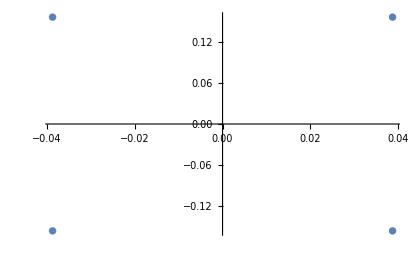

```mathematica
θ=π/3;v=0.5;mD=0.15;ListPlot[{{Re[ⅈ √Πpar[θ,v,mD]],Im[ⅈ √Πpar[θ,v,mD]]},{Re[-ⅈ √Πpar[θ,v,mD]],Im[-ⅈ √Πpar[θ,v,mD]]},{Re[ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[ⅈ √Conjugate[Πpar[θ,v,mD]]]},{Re[-ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[-ⅈ √Conjugate[Πpar[θ,v,mD]]]}}]
```

```mathematica
{{Re[ⅈ √Πpar[θ,v,mD]],Im[ⅈ √Πpar[θ,v,mD]]},{Re[-ⅈ √Πpar[θ,v,mD]],Im[-ⅈ √Πpar[θ,v,mD]]},{Re[ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[ⅈ √Conjugate[Πpar[θ,v,mD]]]},{Re[-ⅈ √Conjugate[Πpar[θ,v,mD]]],Im[-ⅈ √Conjugate[Πpar[θ,v,mD]]]}}
```

{{0.0483963,0.143643},{-0.0483963,-0.143643},{-0.0483963,0.143643},{0.0483963,-0.143643}}

### misc

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

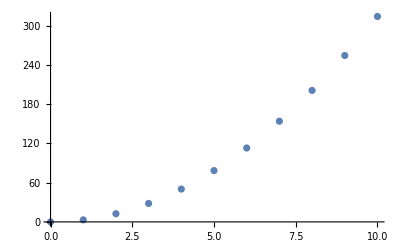

```mathematica
v=0.5;
mD=0.15;
ListPlot[Table[{p,NIntegrate[p^4/(p^2+Πpar[θ,v,mD]),{θ,0,π}]},{p,0,10,1}]]
```

```mathematica
Clear[mD,r,θ];
Assuming[{r Cos[θ]∈Reals,a∈Reals,a>0},Integrate[p^2(p^2+mD^2)/(p^2+z)Exp[ⅈ p r Cos[θ]]Exp[-a p],{p,0,∞}]]
```

ConditionalExpression[1/(2 √π (a-ⅈ r Cos[θ]))(z^(3/2) (a-ⅈ r Cos[θ]) MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},1/4 z (a-ⅈ r Cos[θ])^2]+mD^2 √π (2-a π √z Cos[√z (a-ⅈ r Cos[θ])]+ⅈ π r √z Cos[θ] Cos[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) CosIntegral[√z (a-ⅈ r Cos[θ])] Sin[√z (a-ⅈ r Cos[θ])]+2 √z (a-ⅈ r Cos[θ]) Cos[√z (a-ⅈ r Cos[θ])] SinIntegral[√z (a-ⅈ r Cos[θ])])),(Im[z]≠0&&Re[√z]≠0)||(Re[√z]>0&&Re[z]≥0)]

```mathematica
1/(2 √π (a-ⅈ r Cos[θ]))(z^(3/2) (a-ⅈ r Cos[θ]) MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},1/4 z (a-ⅈ r Cos[θ])^2]+mD^2 √π (2-a π √z Cos[√z (a-ⅈ r Cos[θ])]+ⅈ π r √z Cos[θ] Cos[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) CosIntegral[√z (a-ⅈ r Cos[θ])] Sin[√z (a-ⅈ r Cos[θ])]+2 √z (a-ⅈ r Cos[θ]) Cos[√z (a-ⅈ r Cos[θ])] SinIntegral[√z (a-ⅈ r Cos[θ])]))/.a->0
```

1/(2 √π r)ⅈ Sec[θ] (-ⅈ r z^(3/2) Cos[θ] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]+mD^2 √π (2+ⅈ π r √z Cos[θ] Cosh[r √z Cos[θ]]+2 r √z Cos[θ] CosIntegral[-ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]-2 r √z Cos[θ] Cosh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]))

```mathematica
Clear[mD,r,θ];
Assuming[{r Cos[θ]∈Reals,a∈Reals,a<0},Integrate[p^2(p^2+mD^2)/(p^2+z)Exp[ⅈ p r Cos[θ]]Exp[-a p],{p,-∞,0}]]
```

ConditionalExpression[1/(2 √π (a-ⅈ r Cos[θ]))(z^(3/2) (a-ⅈ r Cos[θ]) MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},1/4 z (a-ⅈ r Cos[θ])^2]-mD^2 √π (2+a π √z Cos[√z (a-ⅈ r Cos[θ])]-ⅈ π r √z Cos[θ] Cos[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) CosIntegral[-√z (a-ⅈ r Cos[θ])] Sin[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) Cos[√z (a-ⅈ r Cos[θ])] SinIntegral[√z (-a+ⅈ r Cos[θ])])),(Im[z]≠0&&Re[√z]≠0)||(Re[√z]>0&&Re[z]≥0)]

```mathematica
1/(2 √π (a-ⅈ r Cos[θ]))(z^(3/2) (a-ⅈ r Cos[θ]) MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},1/4 z (a-ⅈ r Cos[θ])^2]-mD^2 √π (2+a π √z Cos[√z (a-ⅈ r Cos[θ])]-ⅈ π r √z Cos[θ] Cos[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) CosIntegral[-√z (a-ⅈ r Cos[θ])] Sin[√z (a-ⅈ r Cos[θ])]-2 √z (a-ⅈ r Cos[θ]) Cos[√z (a-ⅈ r Cos[θ])] SinIntegral[√z (-a+ⅈ r Cos[θ])]))/.a->0
```

1/(2 √π r)ⅈ Sec[θ] (-ⅈ r z^(3/2) Cos[θ] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]-mD^2 √π (2-ⅈ π r √z Cos[θ] Cosh[r √z Cos[θ]]+2 r √z Cos[θ] CosIntegral[ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]-2 r √z Cos[θ] Cosh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]))

```mathematica
1/(2 √π r)ⅈ Sec[θ] (-ⅈ r z^(3/2) Cos[θ] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]+mD^2 √π (2+ⅈ π r √z Cos[θ] Cosh[r √z Cos[θ]]+2 r √z Cos[θ] CosIntegral[-ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]-2 r √z Cos[θ] Cosh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]))+1/(2 √π r)ⅈ Sec[θ] (-ⅈ r z^(3/2) Cos[θ] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]-mD^2 √π (2-ⅈ π r √z Cos[θ] Cosh[r √z Cos[θ]]+2 r √z Cos[θ] CosIntegral[ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]-2 r √z Cos[θ] Cosh[r √z Cos[θ]] SinhIntegral[r √z Cos[θ]]))//Simplify
```

(√z (z MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 z Cos[θ]^2]-mD^2 √π (π Cosh[r √z Cos[θ]]-ⅈ CosIntegral[-ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]]+ⅈ CosIntegral[ⅈ r √z Cos[θ]] Sinh[r √z Cos[θ]])))/(√π)

```mathematica
rhs[r_,v_,mD_,α_]:=α NIntegrate[Sin[θ] 1/(√π)Re[√Πpar[θ,v,mD] ](Πpar[θ,v,mD] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]-mD^2 √π (π Cosh[r Re[√Πpar[θ,v,mD]]Cos[θ]]-ⅈ CosIntegral[-ⅈ r Re[√Πpar[θ,v,mD]]Cos[θ]] Sinh[r Re[√Πpar[θ,v,mD]]Cos[θ]]+ⅈ CosIntegral[ⅈ r Re[√Πpar[θ,v,mD]]Cos[θ]] Sinh[r Re[√Πpar[θ,v,mD]]Cos[θ]])),{θ,0,π/2}]
```

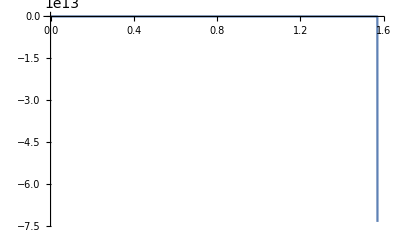

```mathematica
v=0.5;mD=0.15;r=3;Plot[Re[Sin[θ] 1/(√π)Re[√Πpar[θ,v,mD] ](Πpar[θ,v,mD] MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Πpar[θ,v,mD] Cos[θ]^2]-mD^2 √π (π Cosh[r Re[√Πpar[θ,v,mD]]Cos[θ]]-ⅈ CosIntegral[-ⅈ r Re[√Πpar[θ,v,mD]]Cos[θ]] Sinh[r Re[√Πpar[θ,v,mD]]Cos[θ]]+ⅈ CosIntegral[ⅈ r Re[√Πpar[θ,v,mD]]Cos[θ]] Sinh[r Re[√Πpar[θ,v,mD]]Cos[θ]]))],{θ,0,π/2},PlotRange->All]
```